# bow tie ring cavity Mark Saffman 2015.09.13

physical parameters

```mathematica
dir="D:/users/mark/Notes/calculations";
SetDirectory[dir];
<<"marksfunctions.m"
(* SI units *)

hSI = 6.62606896`25 10^-34;
hbarSI = hSI/(2 Pi);
cSI = 299792458; 
mu0 = 4 Pi 10^-7;
epsilon0 = 1/(mu0 cSI^2);

echargeSI = 1.602176487`25 10^-19;
uSI = 1.660538782`25 10^(-27); (* atomic mass unit *)
mSI = 9.10938215`25 10^-31;
mneutronSI = 1.674927211`25 10^-27;
mprotonSI = 1.672621637`25 10^-27;

abohrSI = 5.2917720859`25 10^-11;
mubohrSI = 927.400915`25 10^(-26); (* J/T *)
μBSI = mubohrSI;
munuclearSI = 5.05078324`25 10^(-27); (* J/T *)
μNSI = munuclearSI;
RyinfinitySI = 10973731.568527`25; 
ERySI = hSI cSI RyinfinitySI;(* m^-1 *)
```

## Specify layout

```mathematica
Clear[m,Ltotal,L,L2,Lc,nc,R,λ,nair,waist,L2plot,parms,params15,params20,params25,angle]

nktp=1.84;ntisa=1.77;nknbo3=2.23;nlbo=1.57;

(* parameter sets *)

params1={λ->0.96 10^-6, nair->1,  nc->nktp,Lc->.03,R->.05,L->.399,angle->5 Pi/180};
params2={λ->0.96 10^-6, nair->1,  nc->nktp,Lc->.03,R->.05,L->.39,angle->10 Pi/180};
params3={λ->0.96 10^-6, nair->1,  nc->nktp,Lc->.03,R->.05,L->.41,angle->10 Pi/180};
paramstisa1={λ->0.86 10^-6, nair->1,  nc->ntisa,Lc->.015,R->.04,L->.2};
paramstisa2={λ->0.86 10^-6, nair->1,  nc->ntisa,Lc->.015,R->.04,L->.3};
paramstisa3={λ->0.86 10^-6, nair->1,  nc->ntisa,Lc->.015,R->.04,L->.4};
params4={header->"Toptica SHG100 doubler 960 nm",λ->0.96 10^-6, nair->1,  nc->nknbo3,Lc->.005,R->.025,L->.22+L2,angle->12. Pi/180};

params5={header->"LBO cavity 824 nm",λ-> 0.824 10^-6, nair-> 1,  nc->nlbo,Lc->.02,R->.038,Ltotal->.18,L20->.051, L->Ltotal-L2,angle->9. Pi/180,wBK->32. 10^-6};
params5b={header->"LBO cavity 820 nm",λ->0.821 10^-6, nair->1,  nc->nktp,Lc->.01,R->.05,Ltotal->.4,L2->.05,L->Ltotal-L2,angle->7. Pi/180,wBK->32. 10^-6};
params5c={header->"LBO cavity 920 nm",λ->0.92 10^-6, nair->1,  nc->nlbo,Lc->.01,R->.05,Ltotal->.4,L20->.05,L->Ltotal-L2,angle->7. Pi/180,wBK->32. 10^-6};

params5d={header->"LBO cavity 920 nm, big waist",λ->0.92 10^-6, nair->1,  nc->nktp,Lc->.02,R->.025,Ltotal->.11,L20->.042,L->Ltotal-L2,angle->12. Pi/180,wBK->32. 10^-6,R2->R};

params5e={header->"LBO cavity in place 920 nm, big waist",λ->0.92 10^-6, nair->1,  nc->nktp,Lc->.02,R->.025,Ltotal->.138,L20->.042,L->Ltotal-L2,angle->12.1 Pi/180,wBK->32. 10^-6,R2->R};

params6={header->"PPKTP cavity 820 nm",λ->0.82 10^-6, nair->1,  nc->nktp,Lc->.02,R->.05,R2->R,L->Ltotal-L2,angle->5. Pi/180,Ltotal->.22,L20->.08};

params7={header->"PPKTP cavity 820 nm",λ->0.82 10^-6, nair->1,  nc->nktp,Lc->.02,R->.025,L->Ltotal-L2,angle->12. Pi/180,Ltotal->.135,L20->.037,wBK->22.6 10^-6};

(* ----------------------------- *)
params8={header->"PPKTP cavity 960 nm",λ->0.96 10^-6, nair->1,  nc->nktp,Lc->.03,R->.05,R2->R,angle->8. Pi/180,Ltotal->.26,L20->.068,wBK->29.9 10^-6,L->Ltotal-L2};

params14a={header->"LBO cavity 1540 nm",λ->1.54 10^-6, nair->1,  nc->nlbo,Lc->.03,R->.05,R2->R,angle->8. Pi/180,Ltotal->.27,L20->.067,wBK->40.7 10^-6,L->Ltotal-L2};



(* -------------------------------------- *)

params9={header->"PPKTP cavity 960 nm",λ->0.96 10^-6, nair->1,  nc->nktp,Lc->.03,R->.05,L->Ltotal-L2,angle->12. Pi/180,Ltotal->.135,L20->.037,wBK->24.4 10^(-6)};

params10={header->"PPKTP cavity 920 nm",λ->0.92 10^-6, nair->1,  nc->nktp,Lc->.02,R->.025,L->Ltotal-L2,angle->12. Pi/180,Ltotal->.135,L20->.035,wBK->23.9 10^(-6)};
params11={header->"PPKTP cavity 920 nm",λ->0.92 10^-6, nair->1,  nc->nktp,Lc->.0137,R->.025,L->Ltotal-L2,angle->12. Pi/180,Ltotal->.135,L20->.035,wBK->23.9 10^(-6)};

params12={header->"PPKTP cavity 1196 nm",λ->.92 10^-6, nair->1,  nc->nktp,Lc->.02,R->.025,R2->R,L->Ltotal-L2,angle->12. Pi/180,Ltotal->.13,L20->.037,wBK->27.3 10^(-6)};

parmsLBO990={header->"LBO cavity 990 nm",λ->.99 10^-6, nair->1,  nc->nlbo,Lc->.02,R->.05,R2->R,Rflat->10000000.15,angle->8. Pi/180,Ltotal->.33,L20->.065,wBK->25.7 10^-6,L->Ltotal-L2};

(* L2 (nominal L20) is distance between curved mirrors *)
(* L3 is distance between flat mirrors *)
(* Lc is crystal length *)


(* ------------------------------ Choose parameter set ----------------------------------------- *)
parms=params9;
parms
(* --------------------------------------------------------------------------------------------- *)
```

{header→PPKTP cavity 960 nm,λ→9.6×10^-7,nair→1,nc→1.84,Lc→0.02,R→0.025,L→-L2+Ltotal,angle→0.20944,Ltotal→0.135,L20→0.037,wBK→0.0000244}

## shg 4 mirror (2 concave 2 flat) bowtie cavity analysis

```mathematica
(* standard bowtie - 2 flat 2 curved mirrors *)
L2
L
m=mlinear[Lc/2].mflat[nair,nc].mlinear[(L2-Lc)/2].mmirror[R2].mlinear[L].mmirror[R].mlinear[(L2-Lc)/2].mflat[nc,nair].mlinear[Lc/2];
mt=mlinear[Lc/2].mflat[nair,nc].mlinear[(L2-Lc)/2].mmirrort[R2,angle].mlinear[L].mmirrort[R,angle].mlinear[(L2-Lc)/2].mflat[nc,nair].mlinear[Lc/2];
ms=mlinear[Lc/2].mflat[nair,nc].mlinear[(L2-Lc)/2].mmirrors[R2,angle].mlinear[L].mmirrors[R,angle].mlinear[(L2-Lc)/2].mflat[nc,nair].mlinear[Lc/2];
```

L2

L

```mathematica
(* waists between flat mirrors *)
m2t=mlinear[L/2].mmirrort[R,angle].mlinear[(L2-Lc)/2].mflat[nc,nair].mlinear[Lc].mflat[nair,nc].mlinear[(L2-Lc)/2].mmirrort[R2,angle].mlinear[L/2];
m2s=mlinear[L/2].mmirrors[R,angle].mlinear[(L2-Lc)/2].mflat[nc,nair].mlinear[Lc].mflat[nair,nc].mlinear[(L2-Lc)/2].mmirrors[R2,angle].mlinear[L/2];
```

```mathematica
(* transfer matrix from waist between curved mirrors to waist between flat mirrors *)
m12t= mlinear[L/2].mmirrort[R,angle].mlinear[(L2-Lc)/2].mflat[nc,nair].mlinear[Lc/2];
m12s= mlinear[L/2].mmirrors[R,angle].mlinear[(L2-Lc)/2].mflat[nc,nair].mlinear[Lc/2];
```

```mathematica
m=Simplify[m//.nair->1]; mt=Simplify[mt//.nair->1]; ms=Simplify[ms//.nair->1];
m2t=Simplify[m2t//.nair->1]; m2s=Simplify[m2s//.nair->1];
(*Print[" matrix ",m]*)
A1 = Simplify[m [[1,1]]]; B1= Simplify[m[[1,2]]];D1=Simplify[m[[2,2]]];
ApD=Simplify[A1+D1];
```

```mathematica
A1t = Simplify[mt[[1,1]]]; B1t= Simplify[mt[[1,2]]];D1t=Simplify[mt[[2,2]]];
ApDt=Simplify[A1t+D1t];
A1s = Simplify[ms [[1,1]]]; B1s= Simplify[ms[[1,2]]];D1s=Simplify[ms[[2,2]]];
ApDs=Simplify[A1s+D1s];
```

```mathematica
A2t = Simplify[m2t[[1,1]]]; B2t= Simplify[m2t[[1,2]]];D2t=Simplify[m2t[[2,2]]];
ApD2t=Simplify[A2t+D2t];
A2s = Simplify[m2s [[1,1]]]; B2s= Simplify[m2s[[1,2]]];D2s=Simplify[m2s[[2,2]]];
ApD2s=Simplify[A2s+D2s];
```

```mathematica
radius = Simplify[2 B1/(D1-A1)];
waist = Simplify[ Sqrt[λ/(Pi nc)] Sqrt[2 B1  Sign[B1]] / (4-ApD^2)^(1/4),{nc>0,R>0,R2>0}];
waistt = Simplify[ Sqrt[λ/(Pi nc)] Sqrt[2 B1t  Sign[B1t]] / (4-ApDt^2)^(1/4),{nc>0,R>0,R2>0}];
waists = Simplify[ Sqrt[λ/(Pi nc)] Sqrt[2 B1s  Sign[B1s]] / (4-ApDs^2)^(1/4),{nc>0,R>0,R2>0}];
waist2t = Simplify[ Sqrt[λ/(Pi)] Sqrt[2 B2t  Sign[B2t]] / (4-ApD2t^2)^(1/4),{nc>0,R>0,R2>0}];
waist2s = Simplify[ Sqrt[λ/(Pi)] Sqrt[2 B2s  Sign[B2s]] / (4-ApD2s^2)^(1/4),{nc>0,R>0,R2>0}];
```

```mathematica
waist1=waist//.parms
waist1t=waistt//.parms
waist1s=waists//.parms
waist2t=waist2t//.parms
waist2s=waist2s//.parms
```

(0.01214 √((0.0004 (-0.0123462+0.3249 (0.18-L2))+0.0314 (-0.00082308+(0.04332-1.14 L2) (0.18-L2)+0.04332 L2)+2.4649 ((0.001444-0.038 L2) L2+(0.18-L2) (0.001444-0.076 L2+1. L2^2))) Sign[0.0004 (-0.3249+8.55 (0.18-L2))+0.0314 (-0.02166+(1.14-30. L2) (0.18-L2)+1.14 L2)+2.4649 ((0.038-1. L2) L2+(0.18-L2) (0.038-2. L2+26.3158 L2^2))]))/(4-280.953 (0.02 (2.28-60. (0.18-L2))+1.57 (0.076-4. L2+(0.18-L2) (-4.+105.263 L2)))^2)^(1/4)

(0.00858431 √(-(0.05966 (0.0008664-0.11932 (0.18-L2)-0.11932 L2)+1.01247 (-0.000479812+2.4649 (0.152 (0.18-L2)+0.076 L2) L2)+1.02509 (0.18-L2) (-0.00025992+0.071592 L2-4.9298 L2^2)) Sign[0.05966 (-0.0114+1.57 (0.18-L2)+1.57 L2)+1.01247 (0.00631332+2.4649 (-2. (0.18-L2)-1. L2) L2)+1.02509 (0.18-L2) (0.00342-0.942 L2+64.8658 L2^2)]))/(4-280.953 (0.11932+1.01247 (0.0456+1.57 (-4. (0.18-L2)-4. L2))+1.02509 (0.18-L2) (-1.2+165.263 L2))^2)^(1/4)

(0.00858431 √(-(0.05966 (0.0008664-0.11932 (0.18-L2)-0.11932 L2)+0.987688 (-0.000479812+2.4649 (0.152 (0.18-L2)+0.076 L2) L2)+0.975528 (0.18-L2) (-0.00025992+0.071592 L2-4.9298 L2^2)) Sign[0.05966 (-0.0114+1.57 (0.18-L2)+1.57 L2)+0.987688 (0.00631332+2.4649 (-2. (0.18-L2)-1. L2) L2)+0.975528 (0.18-L2) (0.00342-0.942 L2+64.8658 L2^2)]))/(4-280.953 (0.11932+0.987688 (0.0456+1.57 (-4. (0.18-L2)-4. L2))+0.975528 (0.18-L2) (-1.2+165.263 L2))^2)^(1/4)

(0.0152114 √((1.01247 (0.0008664+1.57 (-0.038 (0.18-L2)-0.076 L2)) (0.18-L2)+0.038 (-0.0004332+0.05966 (0.18-L2)+0.05966 L2)+1.02509 (0.18-L2)^2 (-0.0114+1.57 L2)) Sign[1.01247 (0.0228+1.57 (-1. (0.18-L2)-2. L2)) (0.18-L2)+0.038 (-0.0114+1.57 (0.18-L2)+1.57 L2)+1.02509 (0.18-L2)^2 (-0.3+41.3158 L2)]))/(4-280.953 (0.11932+1.01247 (0.0456+1.57 (-4. (0.18-L2)-4. L2))+1.02509 (0.18-L2) (-1.2+165.263 L2))^2)^(1/4)

(0.0152114 √((0.987688 (0.0008664+1.57 (-0.038 (0.18-L2)-0.076 L2)) (0.18-L2)+0.038 (-0.0004332+0.05966 (0.18-L2)+0.05966 L2)+0.975528 (0.18-L2)^2 (-0.0114+1.57 L2)) Sign[0.987688 (0.0228+1.57 (-1. (0.18-L2)-2. L2)) (0.18-L2)+0.038 (-0.0114+1.57 (0.18-L2)+1.57 L2)+0.975528 (0.18-L2)^2 (-0.3+41.3158 L2)]))/(4-280.953 (0.11932+0.987688 (0.0456+1.57 (-4. (0.18-L2)-4. L2))+0.975528 (0.18-L2) (-1.2+165.263 L2))^2)^(1/4)

```mathematica
(* transfer waists *)
zr1t = Pi nc waist1t^2/λ//.parms 
w2t = waist1t Sqrt[m12t[[1,1]]^2  + m12t[[1,2]]^2/zr1t^2]//.parms
zr1s = Pi nc waist1s^2/λ//.parms 
w2s = waist1s Sqrt[m12s[[1,1]]^2  + m12s[[1,2]]^2/zr1s^2]//.parms
```

-((441.096 (0.05966 (0.0008664-0.11932 (0.18-L2)-0.11932 L2)+1.01247 (-0.000479812+2.4649 (0.152 (0.18-L2)+0.076 L2) L2)+1.02509 (0.18-L2) (-0.00025992+0.071592 L2-4.9298 L2^2)) Sign[0.05966 (-0.0114+1.57 (0.18-L2)+1.57 L2)+1.01247 (0.00631332+2.4649 (-2. (0.18-L2)-1. L2) L2)+1.02509 (0.18-L2) (0.00342-0.942 L2+64.8658 L2^2)])/(√(4-280.953 (0.11932+1.01247 (0.0456+1.57 (-4. (0.18-L2)-4. L2))+1.02509 (0.18-L2) (-1.2+165.263 L2))^2)))

(0.00858431 √((1-26.6438 (0.18-L2))^2+(5.13965×10^-6 (0.01 (1-26.6438 (0.18-L2))+1.57 (1/2 (0.18-L2)+1/2 (1-26.6438 (0.18-L2)) (-0.02+L2)))^2 (4-280.953 (0.11932+1.01247 (0.0456+1.57 (-4. (0.18-L2)-4. L2))+1.02509 (0.18-L2) (-1.2+165.263 L2))^2))/((0.05966 (0.0008664-0.11932 (0.18-L2)-0.11932 L2)+1.01247 (-0.000479812+2.4649 (0.152 (0.18-L2)+0.076 L2) L2)+1.02509 (0.18-L2) (-0.00025992+0.071592 L2-4.9298 L2^2))^2 Sign[0.05966 (-0.0114+1.57 (0.18-L2)+1.57 L2)+1.01247 (0.00631332+2.4649 (-2. (0.18-L2)-1. L2) L2)+1.02509 (0.18-L2) (0.00342-0.942 L2+64.8658 L2^2)]^2)) √(-(0.05966 (0.0008664-0.11932 (0.18-L2)-0.11932 L2)+1.01247 (-0.000479812+2.4649 (0.152 (0.18-L2)+0.076 L2) L2)+1.02509 (0.18-L2) (-0.00025992+0.071592 L2-4.9298 L2^2)) Sign[0.05966 (-0.0114+1.57 (0.18-L2)+1.57 L2)+1.01247 (0.00631332+2.4649 (-2. (0.18-L2)-1. L2) L2)+1.02509 (0.18-L2) (0.00342-0.942 L2+64.8658 L2^2)]))/(4-280.953 (0.11932+1.01247 (0.0456+1.57 (-4. (0.18-L2)-4. L2))+1.02509 (0.18-L2) (-1.2+165.263 L2))^2)^(1/4)

-((441.096 (0.05966 (0.0008664-0.11932 (0.18-L2)-0.11932 L2)+0.987688 (-0.000479812+2.4649 (0.152 (0.18-L2)+0.076 L2) L2)+0.975528 (0.18-L2) (-0.00025992+0.071592 L2-4.9298 L2^2)) Sign[0.05966 (-0.0114+1.57 (0.18-L2)+1.57 L2)+0.987688 (0.00631332+2.4649 (-2. (0.18-L2)-1. L2) L2)+0.975528 (0.18-L2) (0.00342-0.942 L2+64.8658 L2^2)])/(√(4-280.953 (0.11932+0.987688 (0.0456+1.57 (-4. (0.18-L2)-4. L2))+0.975528 (0.18-L2) (-1.2+165.263 L2))^2)))

(0.00858431 √((1-25.9918 (0.18-L2))^2+(5.13965×10^-6 (0.01 (1-25.9918 (0.18-L2))+1.57 (1/2 (0.18-L2)+1/2 (1-25.9918 (0.18-L2)) (-0.02+L2)))^2 (4-280.953 (0.11932+0.987688 (0.0456+1.57 (-4. (0.18-L2)-4. L2))+0.975528 (0.18-L2) (-1.2+165.263 L2))^2))/((0.05966 (0.0008664-0.11932 (0.18-L2)-0.11932 L2)+0.987688 (-0.000479812+2.4649 (0.152 (0.18-L2)+0.076 L2) L2)+0.975528 (0.18-L2) (-0.00025992+0.071592 L2-4.9298 L2^2))^2 Sign[0.05966 (-0.0114+1.57 (0.18-L2)+1.57 L2)+0.987688 (0.00631332+2.4649 (-2. (0.18-L2)-1. L2) L2)+0.975528 (0.18-L2) (0.00342-0.942 L2+64.8658 L2^2)]^2)) √(-(0.05966 (0.0008664-0.11932 (0.18-L2)-0.11932 L2)+0.987688 (-0.000479812+2.4649 (0.152 (0.18-L2)+0.076 L2) L2)+0.975528 (0.18-L2) (-0.00025992+0.071592 L2-4.9298 L2^2)) Sign[0.05966 (-0.0114+1.57 (0.18-L2)+1.57 L2)+0.987688 (0.00631332+2.4649 (-2. (0.18-L2)-1. L2) L2)+0.975528 (0.18-L2) (0.00342-0.942 L2+64.8658 L2^2)]))/(4-280.953 (0.11932+0.987688 (0.0456+1.57 (-4. (0.18-L2)-4. L2))+0.975528 (0.18-L2) (-1.2+165.263 L2))^2)^(1/4)

```mathematica
L2min=(100L20-.75)/.parms
L2max=(100L20+2)/.parms
p1=Plot[{10^6 waist1t//.L2->L2plot/100,10^6 waist1s//.L2->L2plot/100,0  10^4 waist1t 10^6 waist1s//.L2->L2plot/100},
 {L2plot,L2min,L2max},Frame->True,PlotRange->{{L2min,L2max},{20,40}},FrameLabel->{"L2 [cm]","w [mu]"},
PlotStyle->{Dashing[{}],Dashing[{.02,.02}]},PlotLabel->"Tangential and Sagittal waists between curved mirrors",
PlotPoints->50];

p2=Plot[{10^6 w2t//.L2->L2plot/100,10^6 w2s//.L2->L2plot/100},
 {L2plot,L2min,L2max},Frame->True,PlotRange->{{L2min,L2max},{0,300}},FrameLabel->{"L2 [cm]","w [mu]"},
PlotStyle->{Dashing[{}],Dashing[{.02,.02}]},PlotLabel->"Tangential/Sagittal waists between flat mirrors by transfer"];

p22=Plot[{10^6 waist2t//.L2->L2plot/100,10^6 waist2s//.L2->L2plot/100},
 {L2plot,L2min,L2max},Frame->True,PlotRange->{{L2min,L2max},{0,150}},FrameLabel->{"L2 [cm]","w [mu]"},
PlotStyle->{Dashing[{}],Dashing[{.02,.02}]},PlotLabel->"Tangential and Sagittal waists between flat mirrors"];

Ldiag = ((L+L2)/2)(1/(1+Cos[2 angle]));h=Ldiag  Sin[2 angle]//.parms;Lflat = (L - 2 Ldiag)//.parms;
p3=Plot[{(100 Lflat)//.L2->L2plot/100,(100 h)//.L2->L2plot/100},
 {L2plot,L2min,L2max},Frame->True,PlotRange->{{L2min,L2max},{0,15}},FrameLabel->{"L2 [cm]","Lflat, h [cm]"},
PlotStyle->{Dashing[{}],Dashing[{.02,.02}]},PlotLabel->"Distance between flat mirrors, resonator height"];

waistplots=GraphicsRow[{p1,p2,p3},ImageSize->12 72];
```

4.35

7.1

```mathematica
(* cavity picture *)
θ=angle/.parms
L2=L20
Ld=Ltotal/(2(1+Cos[2θ]))//.parms;
xLd=Ld*Cos[2θ]-L2/2 /.θ->angle//.parms;
yLd=Ld*Sin[2θ]//.θ->angle/.parms;
Point1={-L2/2,0}//.parms
Point2={L2/2,0}//.parms
Point3={xLd,yLd}//.parms
Point4={-xLd,yLd}//.parms
l=1.27*10^-2; (* mirror diameter *)
curv= R/.parms; (* curvature radius of concave mirrors *)
arc = 2*ArcSin[l/(2curv)];
```

0.15708

0.051

{-0.0255,0}

{0.0255,0}

{0.0183711,0.0142546}

{-0.0183711,0.0142546}

```mathematica
p1={Point4[[1]]+l/2 Sin[θ],Point4[[2]]+l/2 Cos[θ]};p2={Point4[[1]]-l/2 Sin[θ],Point4[[2]]-l/2 Cos[θ]};
p4 ={Point3[[1]]+l/2 Sin[θ],Point3[[2]]-l/2 Cos[θ]};p3 ={Point3[[1]]-l/2 Sin[θ],Point3[[2]]+l/2 Cos[θ]};
arcX1=(curv*Cos[θ]+Point1[[1]]);
arcY1=(curv*Sin[θ]);
arcX2 =( -curv*Cos[θ]+Point2[[1]]);
arcY2=(curv*Sin[θ]);
```

LBO cavity 824 nm

{header→LBO cavity 824 nm,λ→8.24×10^-7,nair→1,nc→1.57,Lc→0.02,R→0.038,Ltotal→0.18,0.051→0.051,L→-0.051+Ltotal,angle→0.15708,0.000032→0.000032}

total round trip length L_T = 0.18

distance between flat mirrors = 0.0367423

distance between curved mirrors = 0.051

height of resonator (separation of parallel arms) = 0.0142546

length of diagonals = 0.0461289

mirror incidence angle = 9. (deg.)

mirror radii of curvature = 0.038

crystal length = 0.02

B-K optimum waist = 32. (μm)

Center of crystal is at (0,0). Coordinates of the four mirrors are:

{0.0255,0}, {0.0183711,0.0142546}, {-0.0183711,0.0142546}, {-0.0255,0}

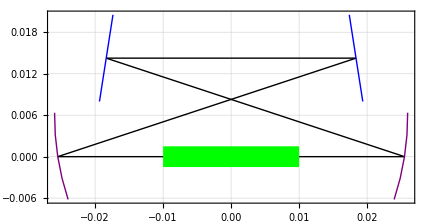

```mathematica
Print[Style[header/.parms,18,Blue]]
parms
Print["total round trip length L_T = ",Ltotal/.parms]
Print["distance between flat mirrors = ",Ltotal-2 Ld-L2/.parms]
Print["distance between curved mirrors = ",L2/.parms]
Print["height of resonator (separation of parallel arms) = ",Ld Sin[2θ]]
Print["length of diagonals = ",Ld]
Print["mirror incidence angle = ",angle 180/π/.parms," (deg.)"]
Print["mirror radii of curvature = ",R/.parms]
Print["crystal length = ",Lc/.parms]
Print["B-K optimum waist = ",10^6 wBK/.parms," (μm)"]
Print[]
Print["Center of crystal is at (0,0). Coordinates of the four mirrors are:"]
Print[Point2,", ",Point3,", ",Point4,", ",Point1]
Graphics[{Line[{Point1,Point2}],Line[{Point2,Point4}],Line[{Point4,Point3}],Line[{Point3,Point1}],Thick,Green,Rectangle[{- Lc/2/.parms,-0.0015},{Lc/2/.parms,0.0015}],Blue,Line[{p1,p2}],Line[{p3,p4}],Purple,Circle[{arcX1,arcY1},curv,{θ+π-arc/2,θ+π+arc/2}],Circle[{arcX2,arcY2},curv,{2π-θ-arc/2,2π-θ+arc/2}]},Frame->True,GridLines->Automatic,ImageMargins->1,ImageSize->6 72]
waistplots
```

```mathematica
Export["/Users/williammilner/Downloads/LBOHolmiumResonator.jpg",%1717,"JPEG"]
```

/Users/williammilner/Downloads/LBOHolmiumResonator.jpg

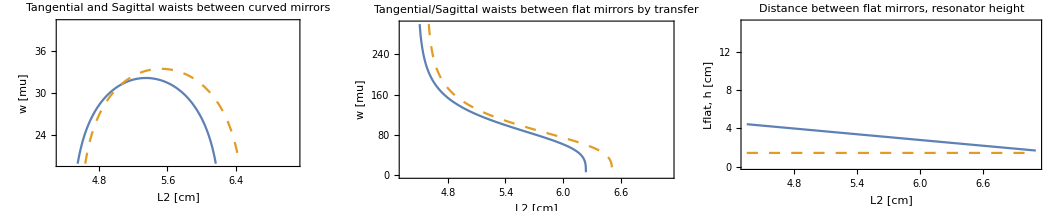

```mathematica
Export["/Users/williammilner/Downloads/LBOWaistPropagation.jpg",%1718,"JPEG"]
```

/Users/williammilner/Downloads/LBOWaistPropagation.jpg

## shg 4 mirror (2 concave 2 convex) bowtie cavity analysis

LBO cavity 990 nm

{header→LBO cavity 990 nm,λ→9.9×10^-7,nair→1,nc→1.57,Lc→0.02,R→0.05,R2→R,Rflat→1.×10^7,angle→0.139626,Ltotal→0.33,L20→0.065,wBK→0.0000257,L→-L2+Ltotal}

total round trip length L_T = 0.33

distance between flat mirrors = 0.156642-L2

distance between curved mirrors = L2

height of resonator (separation of parallel arms) = 0.0238919

length of diagonals = 0.0866789

mirror incidence angle = 8. (deg.)

mirror radii of curvature = 0.05

flat mirror radii of curvature = 1.×10^7

crystal length = 0.02

B-K optimum waist = 25.7 (μm)

point1

point2

point3

point4

0.139626

L20

{-0.0325,0}

{0.0325,0}

{0.0483705,0.0231892}

{-0.0483705,0.0231892}

Center of crystal is at (0,0). Coordinates of the four mirrors are:

{0.0325,0}, {0.0483705,0.0231892}, {-0.0483705,0.0231892}, {-0.0325,0}

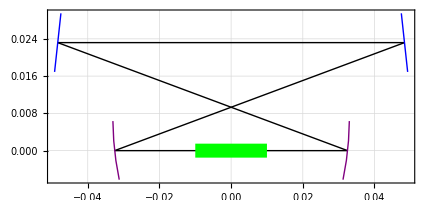

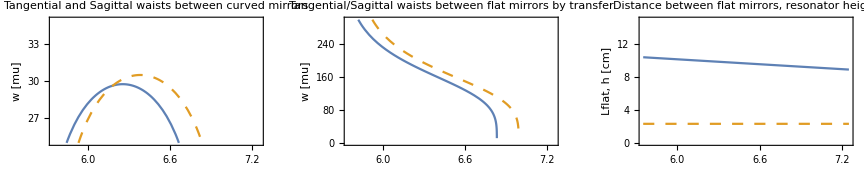

```mathematica
Clear[m,L,L2,Lc,nc,R,λ,nair,waist,L2plot,angle]
Print[Style[header/.parms,18,Blue]]
parms
Print["total round trip length L_T = ",Ltotal/.parms]
Print["distance between flat mirrors = ",Ltotal-2 Ld-L2/.parms]
Print["distance between curved mirrors = ",L2/.parms]
Print["height of resonator (separation of parallel arms) = ",Ld Sin[2θ]]
Print["length of diagonals = ",Ld]
Print["mirror incidence angle = ",angle 180/π/.parms," (deg.)"]
Print["mirror radii of curvature = ",R/.parms]
Print["flat mirror radii of curvature = ",Rflat/.parms]
Print["crystal length = ",Lc/.parms]
Print["B-K optimum waist = ",10^6 wBK/.parms," (μm)"]
Print[]

Ldiag = ((L+L2)/2)(1/(1+Cos[2 angle]));h=Ldiag  Sin[2 angle]//.parms;Lflat = (L - 2 Ldiag)//.parms;
mside=mlinear[Ldiag].mmirror[Rflat].mlinear[Lflat].mmirror[Rflat].mlinear[Ldiag];
msidet=mlinear[Ldiag].mmirrort[Rflat,angle].mlinear[Lflat].mmirrort[Rflat,angle].mlinear[Ldiag];
msides=mlinear[Ldiag].mmirrors[Rflat,angle].mlinear[Lflat].mmirrors[Rflat,angle].mlinear[Ldiag];
m=mlinear[Lc/2].mflat[nair,nc].mlinear[(L2-Lc)/2].mmirror[R2].mside.mmirror[R].mlinear[(L2-Lc)/2].mflat[nc,nair].mlinear[Lc/2];
mt=mlinear[Lc/2].mflat[nair,nc].mlinear[(L2-Lc)/2].mmirrort[R2,angle].msidet.mmirrort[R,angle].mlinear[(L2-Lc)/2].mflat[nc,nair].mlinear[Lc/2];
ms=mlinear[Lc/2].mflat[nair,nc].mlinear[(L2-Lc)/2].mmirrors[R2,angle].msides.mmirrors[R,angle].mlinear[(L2-Lc)/2].mflat[nc,nair].mlinear[Lc/2];

(* waists between flat mirrors *)
m2t=mlinear[L/2].mmirrort[R,angle].mlinear[(L2-Lc)/2].mflat[nc,nair].mlinear[Lc].mflat[nair,nc].mlinear[(L2-Lc)/2].mmirrort[R2,angle].mlinear[L/2];
m2s=mlinear[L/2].mmirrors[R,angle].mlinear[(L2-Lc)/2].mflat[nc,nair].mlinear[Lc].mflat[nair,nc].mlinear[(L2-Lc)/2].mmirrors[R2,angle].mlinear[L/2];

(* transfer matrix from waist between curved mirrors to waist between flat mirrors *)
m12t= mlinear[L/2].mmirrort[R,angle].mlinear[(L2-Lc)/2].mflat[nc,nair].mlinear[Lc/2];
m12s= mlinear[L/2].mmirrors[R,angle].mlinear[(L2-Lc)/2].mflat[nc,nair].mlinear[Lc/2];
Print["point1"]

m=m//.nair->1; mt=mt//.nair->1; ms=ms//.nair->1;m2t=m2t//.nair->1; m2s=m2s//.nair->1;
(* Print["m matrix ",m//.parms]*)
A1 = m [[1,1]]; B1= m[[1,2]];D1=m[[2,2]];ApD=A1+D1;
Print["point2"]

A1t = mt[[1,1]]; B1t= mt[[1,2]]; D1t=mt[[2,2]];ApDt=A1t+D1t;
A1s = ms [[1,1]]; B1s= ms[[1,2]]; D1s=ms[[2,2]];ApDs=A1s+D1s;

Print["point3"]

radius =2 B1/(D1-A1);
waist = Sqrt[λ/(Pi nc)] Sqrt[2 B1  Sign[B1]] / (4-ApD^2)^(1/4);
waistt = Sqrt[λ/(Pi nc)] Sqrt[2 B1t  Sign[B1t]] / (4-ApDt^2)^(1/4);
waists = Sqrt[λ/(Pi nc)] Sqrt[2 B1s  Sign[B1s]] / (4-ApDs^2)^(1/4);
waist1=waist//.parms;waist1t=waistt//.parms;waist1s=waists//.parms;  
Print["point4"]
(* 
A2t = Simplify[m2t[[1,1]]]; B2t= Simplify[m2t[[1,2]]]; D2t=Simplify[m2t[[2,2]]];ApD2t=A2t+D2t;
A2s = Simplify[m2s [[1,1]]]; B2s= Simplify[m2s[[1,2]]]; D2s=Simplify[m2s[[2,2]]];ApD2s=A2s+D2s;waist2t = Simplify[ Sqrt[λ/(Pi)] Sqrt[2 B2t  Sign[B2t]] / (4-ApD2t^2)^(1/4),{nc>0,R>0,R2>0}];
waist2s = Simplify[ Sqrt[λ/(Pi)] Sqrt[2 B2s  Sign[B2s]] / (4-ApD2s^2)^(1/4),{nc>0,R>0,R2>0}];waist2t=waist2t//.parms;waist2s=waist2s//.parms;  *)


(* transfer waists *)
zr1t = Pi nc waist1t^2/λ//.parms ;
w2t = waist1t Sqrt[m12t[[1,1]]^2  + m12t[[1,2]]^2/zr1t^2]//.parms;
zr1s = Pi nc waist1s^2/λ//.parms ;
w2s = waist1s Sqrt[m12s[[1,1]]^2  + m12s[[1,2]]^2/zr1s^2]//.parms;


L2min=(100L20-.75)/.parms; L2max=(100L20+.75)/.parms;

p1=Plot[{10^6 waist1t//.L2->L2plot/100,10^6 waist1s//.L2->L2plot/100,0  10^4 waist1t 10^6 waist1s//.L2->L2plot/100},
 {L2plot,L2min,L2max},Frame->True,PlotRange->{{L2min,L2max},{25,35}},FrameLabel->{"L2 [cm]","w [mu]"},
PlotStyle->{Dashing[{}],Dashing[{.02,.02}]},PlotLabel->"Tangential and Sagittal waists between curved mirrors",
PlotPoints->50];

p2=Plot[{10^6 w2t//.L2->L2plot/100,10^6 w2s//.L2->L2plot/100},
 {L2plot,L2min,L2max},Frame->True,PlotRange->{{L2min,L2max},{0,300}},FrameLabel->{"L2 [cm]","w [mu]"},
PlotStyle->{Dashing[{}],Dashing[{.02,.02}]},PlotLabel->"Tangential/Sagittal waists between flat mirrors by transfer"];
(*
p22=Plot[{10^6 waist2t//.L2->L2plot/100,10^6 waist2s//.L2->L2plot/100},
 {L2plot,L2min,L2max},Frame->True,PlotRange->{{L2min,L2max},{0,150}},FrameLabel->{"L2 [cm]","w [mu]"},
PlotStyle->{Dashing[{}],Dashing[{.02,.02}]},PlotLabel->"Tangential and Sagittal waists between flat mirrors"];
*)

Ldiag = ((L+L2)/2)(1/(1+Cos[2 angle]));h=Ldiag  Sin[2 angle]//.parms;Lflat = (L - 2 Ldiag)//.parms;
p3=Plot[{(100 Lflat)//.L2->L2plot/100,(100 h)//.L2->L2plot/100},
 {L2plot,L2min,L2max},Frame->True,PlotRange->{{L2min,L2max},{0,15}},FrameLabel->{"L2 [cm]","Lflat, h [cm]"},
PlotStyle->{Dashing[{}],Dashing[{.02,.02}]},PlotLabel->"Distance between flat mirrors, resonator height"];

waistplots=GraphicsRow[{p1,p2,p3},ImageSize->12 72];


(* cavity picture *)
θ=angle/.parms
L2=L20
Ld=Ltotal/(2(1+Cos[2θ]))//.parms;
xLd=Ld*Cos[2θ]-L2/2 /.θ->angle//.parms;
yLd=Ld*Sin[2θ]//.θ->angle/.parms;
Point1={-L2/2,0}//.parms
Point2={L2/2,0}//.parms
Point3={xLd,yLd}//.parms
Point4={-xLd,yLd}//.parms
l=1.27*10^-2; (* mirror diameter *)
curv= R/.parms; (* curvature radius of concave mirrors *)
arc = 2*ArcSin[l/(2curv)];
p1={Point4[[1]]+l/2 Sin[θ],Point4[[2]]+l/2 Cos[θ]};p2={Point4[[1]]-l/2 Sin[θ],Point4[[2]]-l/2 Cos[θ]};
p4 ={Point3[[1]]+l/2 Sin[θ],Point3[[2]]-l/2 Cos[θ]};p3 ={Point3[[1]]-l/2 Sin[θ],Point3[[2]]+l/2 Cos[θ]};
arcX1=(curv*Cos[θ]+Point1[[1]]);
arcY1=(curv*Sin[θ]);
arcX2 =( -curv*Cos[θ]+Point2[[1]]);
arcY2=(curv*Sin[θ]);



Print["Center of crystal is at (0,0). Coordinates of the four mirrors are:"]
Print[Point2,", ",Point3,", ",Point4,", ",Point1]
Graphics[{Line[{Point1,Point2}],Line[{Point2,Point4}],Line[{Point4,Point3}],Line[{Point3,Point1}],Thick,Green,Rectangle[{- Lc/2/.parms,-0.0015},{Lc/2/.parms,0.0015}],Blue,Line[{p1,p2}],Line[{p3,p4}],Purple,Circle[{arcX1,arcY1},curv,{θ+π-arc/2,θ+π+arc/2}],Circle[{arcX2,arcY2},curv,{2π-θ-arc/2,2π-θ+arc/2}]},Frame->True,GridLines->Automatic,ImageMargins->1,ImageSize->6 72]
waistplots
```

Brewster cut crystal

```mathematica
Lc = .01 ; (* crystal optical path length *)
nc=1.57;
θB=ArcTan[nc]; Print["θB = ",θB 180/π, " deg"]
θBp=ArcTan[1/nc];  Print["θBp = ",θBp 180/π, " deg"]
θa=θB-θBp; Print["θa = ",θa 180/π, " deg"]
tx=Lc Cos[θa];
ty=Lc Sin[θa];
tc=Lc Cos[θBp];
Print["Lc = ",Lc,", tx = ",tx,", ty = ",ty,", tc = ",tc]
```

θB = 57.5052 deg

θBp = 32.4948 deg

θa = 25.0104 deg

Lc = 0.01, tx = 0.00906231, ty = 0.00422783, tc = 0.0084344

## shg 2 mirror + brewster crystal cavity mode waists and layout

```mathematica
Clear[m,L,L2,Lc,nc,R,λ,nair,waist,L2plot,params,params15,params20,params25,angle]

nktp=1.84;ntisa=1.77;nknbo3=2.23;nlbo=1.57;

(* parameter sets *)

parms1={header->"LBO cavity 820 nm",λ->0.821 10^-6, nair->1,  nc->nlbo,Lc->.02,R->.03,R2->R 1.0,Ltotal->.2,L20->.055,L->Ltotal-L2,angle->25. Pi/180,wBK->32. 10^-6,θB->ArcTan[nc],θBp->ArcTan[1/nc]}
(* L20 is distance between curved mirrors *)
(* Lc is crystal length *)

(* ------------------------------ Choose parameter set ----------------------------------------- *)
parms=parms1;
(* --------------------------------------------------------------------------------------------- *)

(*  Brewster crystal, 2 curved mirrors *)

(* waist in crystal *)

mt=mlinear[Lc/2].mflatt[nair,nc,Infinity,θB].mlinear[(L2-Lc)/2].mmirrort[R2,angle].mlinear[L].mmirrort[R,angle].mlinear[(L2-Lc)/2].mflatt[nc,nair,Infinity,-θBp].mlinear[Lc/2];
ms=mlinear[Lc/2].mflat[nair,nc].mlinear[(L2-Lc)/2].mmirrors[R2,angle].mlinear[L].mmirrors[R,angle].mlinear[(L2-Lc)/2].mflat[nc,nair].mlinear[Lc/2];
(*
(* waist in air *)
m2t=mlinear[L/2].mmirrort[R,angle].mlinear[(L2-Lc)/2].mflat[nc,nair].mlinear[Lc].mflat[nair,nc].mlinear[(L2-Lc)/2].mmirrort[R2,angle].mlinear[L/2];
m2s=mlinear[L/2].mmirrors[R,angle].mlinear[(L2-Lc)/2].mflat[nc,nair].mlinear[Lc].mflat[nair,nc].mlinear[(L2-Lc)/2].mmirrors[R2,angle].mlinear[L/2];
*)


mt=Simplify[mt//.parms]; ms=Simplify[ms//.parms];
(* m2t=Simplify[m2t//.parms]; m2s=Simplify[m2s//.parms]; *)

A1t = Simplify[mt[[1,1]]]; B1t= Simplify[mt[[1,2]]]; D1t=Simplify[mt[[2,2]]];
ApDt=Simplify[A1t+D1t];
A1s = Simplify[ms [[1,1]]]; B1s= Simplify[ms[[1,2]]];D1s=Simplify[ms[[2,2]]];
ApDs=Simplify[A1s+D1s];

(*
A2t = Simplify[m2t[[1,1]]]; B2t= Simplify[m2t[[1,2]]];D2t=Simplify[m2t[[2,2]]];
ApD2t=Simplify[A2t+D2t];
A2s = Simplify[m2s [[1,1]]]; B2s= Simplify[m2s[[1,2]]]; D2s=Simplify[m2s[[2,2]]];
ApD2s=Simplify[A2s+D2s];
*)

radius = Simplify[2 B1/(D1-A1)];
waist1t = Simplify[ Sqrt[λ/(Pi nc)] Sqrt[2 B1t  Sign[B1t]] / (4-ApDt^2)^(1/4),{nc>0,R>0,R2>0}];
waist1s = Simplify[ Sqrt[λ/(Pi nc)] Sqrt[2 B1s  Sign[B1s]] / (4-ApDs^2)^(1/4),{nc>0,R>0,R2>0}];
waist2t = Simplify[ Sqrt[λ/(Pi)] Sqrt[2 B2t  Sign[B2t]] / (4-ApD2t^2)^(1/4),{nc>0,R>0,R2>0}];
waist2s = Simplify[ Sqrt[λ/(Pi)] Sqrt[2 B2s  Sign[B2s]] / (4-ApD2s^2)^(1/4),{nc>0,R>0,R2>0}];

waist1t=waist1t//.parms;
waist1s=waist1s//.parms;  
waist2t=waist2t//.parms;
waist2s=waist2s//.parms;  



L2min=(100L20-2)/.parms; L2max=(100L20+2)/.parms;
p1=Plot[{10^6 waist1t//.L2->L2plot/100,10^6 waist1s//.L2->L2plot/100,0  10^4 waist1t 10^6 waist1s//.L2->L2plot/100},
 {L2plot,L2min,L2max},Frame->True,PlotRange->{{L2min,L2max},{0,50}},FrameLabel->{"L2 [cm]","w [mu]"},
PlotStyle->{Dashing[{}],Dashing[{.02,.02}]},PlotLabel->"Tangential and Sagittal waists between curved mirrors",
PlotPoints->50]
(*

p2=Plot[{10^6 w2t//.L2->L2plot/100,10^6 w2s//.L2->L2plot/100},
 {L2plot,L2min,L2max},Frame->True,PlotRange->{{L2min,L2max},{0,150}},FrameLabel->{"L2 [cm]","w [mu]"},
PlotStyle->{Dashing[{}],Dashing[{.02,.02}]},PlotLabel->"Tangential/Sagittal waists between flat mirrors by transfer"];

p22=Plot[{10^6 waist2t//.L2->L2plot/100,10^6 waist2s//.L2->L2plot/100},
 {L2plot,L2min,L2max},Frame->True,PlotRange->{{L2min,L2max},{0,150}},FrameLabel->{"L2 [cm]","w [mu]"},
PlotStyle->{Dashing[{}],Dashing[{.02,.02}]},PlotLabel->"Tangential and Sagittal waists between flat mirrors"];

Ldiag = ((L+L2)/2)(1/(1+Cos[2 angle]));h=Ldiag  Sin[2 angle]//.parms;Lflat = (L - 2 Ldiag)//.parms;
p3=Plot[{(100 Lflat)//.L2->L2plot/100,(100 h)//.L2->L2plot/100},
 {L2plot,L2min,L2max},Frame->True,PlotRange->{{L2min,L2max},{0,15}},FrameLabel->{"L2 [cm]","Lflat, h [cm]"},
PlotStyle->{Dashing[{}],Dashing[{.02,.02}]},PlotLabel->"Distance between flat mirrors, resonator height"];

waistplots=GraphicsRow[{p1,p2,p22,p3},ImageSize->12 72];
*)


(* cavity picture *)
θ=angle/.parms
L2=L20
Ld=Ltotal/(2(1+Cos[2θ]))//.parms;
xLd=Ld*Cos[2θ]-L2/2 /.θ->angle//.parms;
yLd=Ld*Sin[2θ]//.θ->angle/.parms;
Point1={-L2/2,0}//.parms
Point2={L2/2,0}//.parms
Point3={xLd,yLd}//.parms
Point4={-xLd,yLd}//.parms
l=1.27*10^-2; (* mirror diameter *)
curv= R/.parms; (* curvature radius of concave mirrors *)
arc = 2*ArcSin[l/(2curv)];
p1={Point4[[1]]+l/2 Sin[θ],Point4[[2]]+l/2 Cos[θ]};p2={Point4[[1]]-l/2 Sin[θ],Point4[[2]]-l/2 Cos[θ]};
p4 ={Point3[[1]]+l/2 Sin[θ],Point3[[2]]-l/2 Cos[θ]};p3 ={Point3[[1]]-l/2 Sin[θ],Point3[[2]]+l/2 Cos[θ]};
arcX1=(curv*Cos[θ]+Point1[[1]]);
arcY1=(curv*Sin[θ]);
arcX2 =( -curv*Cos[θ]+Point2[[1]]);
arcY2=(curv*Sin[θ]);


Print[Style[header/.parms,18,Blue]]
parms
Print["total round trip length L_T = ",Ltotal/.parms]
Print["distance between flat mirrors = ",Ltotal-2 Ld-L2/.parms]
Print["distance between curved mirrors = ",L2/.parms]
Print["height of resonator (separation of parallel arms) = ",Ld Sin[2θ]]
Print["length of diagonals = ",Ld]
Print["mirror incidence angle = ",angle 180/π/.parms," (deg.)"]
Print["mirror radii of curvature = ",R/.parms]
Print["crystal length = ",Lc/.parms]
Print["B-K optimum waist = ",10^6 wBK/.parms," (μm)"]
Print[]
Print["Center of crystal is at (0,0). Coordinates of the four mirrors are:"]
Print[Point2,", ",Point3,", ",Point4,", ",Point1]
Graphics[{Line[{Point1,Point2}],Line[{Point2,Point4}],Line[{Point4,Point3}],Line[{Point3,Point1}],Thick,Green,Rectangle[{- Lc/2/.parms,-0.0015},{Lc/2/.parms,0.0015}],Blue,Line[{p1,p2}],Line[{p3,p4}],Purple,Circle[{arcX1,arcY1},curv,{θ+π-arc/2,θ+π+arc/2}],Circle[{arcX2,arcY2},curv,{2π-θ-arc/2,2π-θ+arc/2}]},Frame->True,GridLines->Automatic,ImageMargins->1,ImageSize->6 72]
waistplots
```

{header→LBO cavity 820 nm,λ→8.21×10^-7,nair→1,nc→1.57,Lc→0.02,R→0.03,R2→1. R,Ltotal→0.2,L20→0.055,L→-L2+Ltotal,angle→0.436332,wBK→0.000032,1.00366→ArcTan[nc],0.567141→ArcTan[1/nc]}

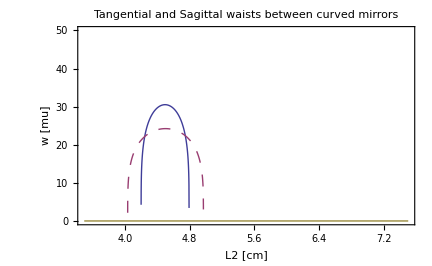

0.436332

L20

{-0.0275,0}

{0.0275,0}

{0.0116279,0.0466308}

{-0.0116279,0.0466308}

LBO cavity 820 nm

{header→LBO cavity 820 nm,λ→8.21×10^-7,nair→1,nc→1.57,Lc→0.02,R→0.03,R2→1. R,Ltotal→0.2,L20→0.055,L→-L20+Ltotal,angle→0.436332,wBK→0.000032,1.00366→ArcTan[nc],0.567141→ArcTan[1/nc]}

total round trip length L_T = 0.2

distance between flat mirrors = 0.0232557

distance between curved mirrors = 0.055

height of resonator (separation of parallel arms) = 0.0466308

length of diagonals = 0.0608721

mirror incidence angle = 25. (deg.)

mirror radii of curvature = 0.03

crystal length = 0.02

B-K optimum waist = 32. (μm)

Center of crystal is at (0,0). Coordinates of the four mirrors are:

{0.0275,0}, {0.0116279,0.0466308}, {-0.0116279,0.0466308}, {-0.0275,0}

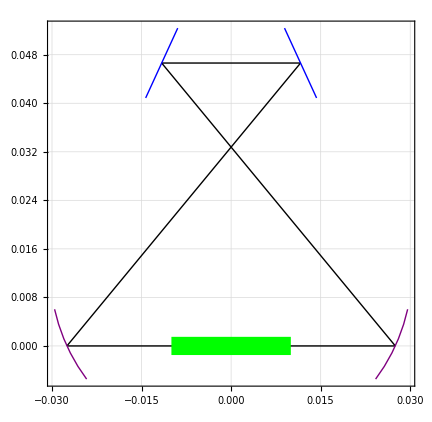

waistplots

## P2 generated in cavity PPKTP

ENLbk = 0.0582297

Using ENL = 0.0582297

9

T1/(1-√(1-loss))^2

PPKTP, 2 cm λ=1.196 μm

w BK = 30.4084 (μm)

ENL BK optimum = 0.0582297

Power build up factor in cavity (no SHG generated) = 597.938

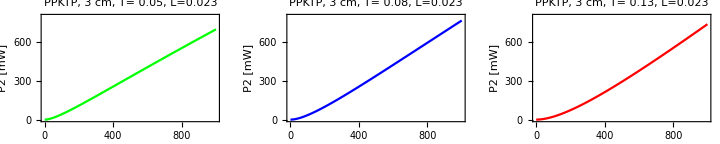

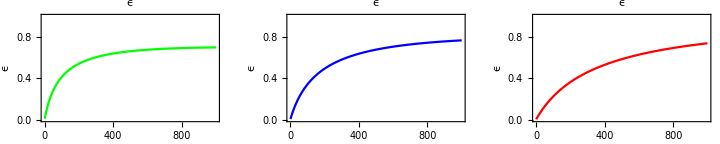

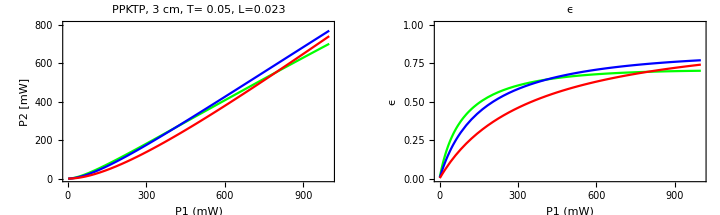

```mathematica
Clear[T1,loss,P2overP1,Enl,P1,P2,passes,P2out]

(* PPKTP *)

deff=9.8 10^(-12);
n1=1.8;
n2=1.8;
lambda1=1.198 10^(-6);
lambda1=.99 10^(-6);
omega1=2 π cSI/lambda1;
Lc=0.03;
ENLbk=1.068 2 omega1^3 deff^2 Lc/(π epsilon0 cSI^4 n1 n2);
Print["ENLbk = ",ENLbk]
(* ENLbk=0.01; (* PPKTP 2 cm, 920 nm, w=60 micron *) *)
Print["Using ENL = ",ENLbk]
lossv1=2 .001 +0.0007+2 .005;
lossv1=3 .001 +2 .005 +.01;
focusfactor=3^2
label="PPKTP, 3 cm";
parmsppktp = {header->label,P1->.2,T1->.08,loss->lossv1};
parmsppktppower={header->label,Enl->ENLbk/focusfactor,T1->.05,loss->lossv1};
parmsppktppower2={header->label,Enl->ENLbk/focusfactor,T1->.08,loss->lossv1};
parmsppktppower3={header->label,Enl->ENLbk/focusfactor,T1->.13,loss->lossv1};



(* --------------------------- choose parameter set ------------------------------------ *)
parms=parmsppktp;
parmspower=parmsppktppower;
parmspower2=parmsppktppower2;
parmspower3=parmsppktppower3;
(* --------------------------------------------------------------------------------------- *)

eq={P2overP1==16  T1^2  Enl P1/(2-Sqrt[1-T1](2-loss- passes Sqrt[P2overP1  Enl P1]))^4};
p2maxinmw=5.;  (* max. output power for plotting *)
enlmax=.03; (* for plotting *)
passes=1 ;  (* 1 for unidirectional ring, 2 for bidirectional linear cavity *)
sol1=Solve[eq/.parms,{P2overP1}];

P1max=1000; P2max=.8 P1max;
P2out = P1 P2overP1/.Solve[eq/.parmspower,{P2overP1}][[1]];
plotlabel=StringJoin[header/.parmspower,", T= ",ToString[T1/.parmspower],", L=",ToString[loss/.parmspower]];
p1=Plot[10^3 P2out//.{P1->.001 P1mW} ,{P1mW,1,P1max},Frame->True,FrameLabel->{"P1 (mW)","P2 [mW]"},PlotLabel->plotlabel,PlotRange->{{0,P1max},{0, P2max}},BaseStyle->{FontWeight->"Bold",FontSize->12,FontFamily->"Arial"},FrameStyle->AbsoluteThickness[1.],Ticks->AbsoluteThickness[4.],PlotStyle->Green];

peps1=Plot[(P2out/P1)//.{P1->.001 P1mW} ,{P1mW,1,P1max},Frame->True,FrameLabel->{"P1 (mW)","ϵ"},PlotLabel->"ϵ",PlotRange->{{0,P1max},{0,1}},BaseStyle->{FontWeight->"Bold",FontSize->12,FontFamily->"Arial"},FrameStyle->AbsoluteThickness[1.],Ticks->AbsoluteThickness[4.],ImageSize->5 72,PlotStyle->Green];

P2out = P1 P2overP1/.Solve[eq/.parmspower2,{P2overP1}][[1]];
plotlabel=StringJoin[header/.parmspower2,", T= ",ToString[T1/.parmspower2],", L=",ToString[loss/.parmspower2]];
p2=Plot[10^3 P2out//.{P1->.001 P1mW} ,{P1mW,1,P1max},Frame->True,FrameLabel->{"P1 (mW)","P2 [mW]"},PlotLabel->plotlabel,PlotRange->{{0,P1max},{0, P2max}},BaseStyle->{FontWeight->"Bold",FontSize->12,FontFamily->"Arial"},FrameStyle->AbsoluteThickness[1.],Ticks->AbsoluteThickness[4.],PlotStyle->Blue];

peps2=Plot[(P2out/P1)//.{P1->.001 P1mW} ,{P1mW,1,P1max},Frame->True,FrameLabel->{"P1 (mW)","ϵ"},PlotLabel->"ϵ",PlotRange->{{0,P1max},{0,1}},BaseStyle->{FontWeight->"Bold",FontSize->12,FontFamily->"Arial"},FrameStyle->AbsoluteThickness[1.],Ticks->AbsoluteThickness[4.],PlotStyle->Blue,ImageSize->5 72];

P2out = P1 P2overP1/.Solve[eq/.parmspower3,{P2overP1}][[1]];
plotlabel=StringJoin[header/.parmspower3,", T= ",ToString[T1/.parmspower3],", L=",ToString[loss/.parmspower3]];
p3=Plot[10^3 P2out//.{P1->.001 P1mW} ,{P1mW,1,P1max},Frame->True,FrameLabel->{"P1 (mW)","P2 [mW]"},PlotLabel->plotlabel,PlotRange->{{0,P1max},{0, P2max}},BaseStyle->{FontWeight->"Bold",FontSize->12,FontFamily->"Arial"},FrameStyle->AbsoluteThickness[1.],Ticks->AbsoluteThickness[4.],PlotStyle->Red];

peps3=Plot[(P2out/P1)//.{P1->.001 P1mW} ,{P1mW,1,P1max},Frame->True,FrameLabel->{"P1 (mW)","ϵ"},PlotLabel->"ϵ",PlotRange->{{0,P1max},{0,1}},BaseStyle->{FontWeight->"Bold",FontSize->12,FontFamily->"Arial"},FrameStyle->AbsoluteThickness[1.],Ticks->AbsoluteThickness[4.],PlotStyle->Red,ImageSize->5 72];
buildup = T1/(1-Sqrt[1-loss])^2
Print["PPKTP, 2 cm λ=1.196 μm"] 
Print["w BK = ",10^6 Sqrt[lambda1 Lc/(5.68 π n1)]," (μm)"]
Print["ENL BK optimum = ",ENLbk]
Print["Power build up factor in cavity (no SHG generated) = ",buildup//.parms]
GraphicsRow[{p1,p2,p3},ImageSize->10 72]
GraphicsRow[{peps1,peps2,peps3},ImageSize->10 72]
p1=Show[p1,p2,p3,ImageSize->5 72,PlotRange->{{0,P1max},{0, P2max}}];
p2=Show[peps1,peps2,peps3,ImageSize->5 72,PlotRange->{{0,P1max},{0,1}}];
GraphicsRow[{p1,p2},ImageSize->10 72]
```

## P2 generated in cavity LBO

ENLbk = 0.000258691

Using ENL = 0.000258691

{header→LBO NCPM 2 cm,Enl→0.000155214,T1→0.03,loss→0.013}

{header→LBO NCPM 2 cm,Enl→0.000155214,T1→0.04,loss→0.013}

{header→LBO NCPM 2 cm,Enl→0.000155214,T1→0.05,loss→0.013}

{header→LBO NCPM 2 cm,Enl→0.000155214,T1→0.015,loss→0.013}

{header→LBO NCPM 2 cm,Enl→0.000155214,T1→0.02,loss→0.013}

{header→LBO NCPM 2 cm,Enl→0.000155214,T1→0.025,loss→0.013}

{header→LBO NCPM 2 cm,Enl→0.000155214,T1→0.03,loss→0.013}

{header→LBO NCPM 2 cm,Enl→0.000155214,T1→0.035,loss→0.013}

T1/(1-√(1-loss))^2

LBO, 2 cm

w BK = 26.5848 (μm)

ENL BK optimum = 0.000155214

Power build up factor in cavity (no SHG generated) = 352.718

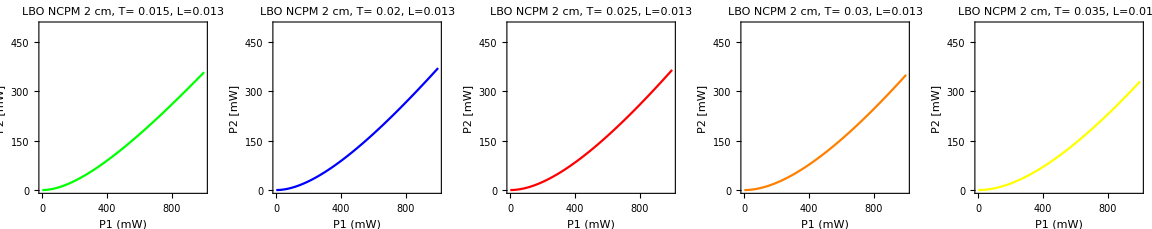

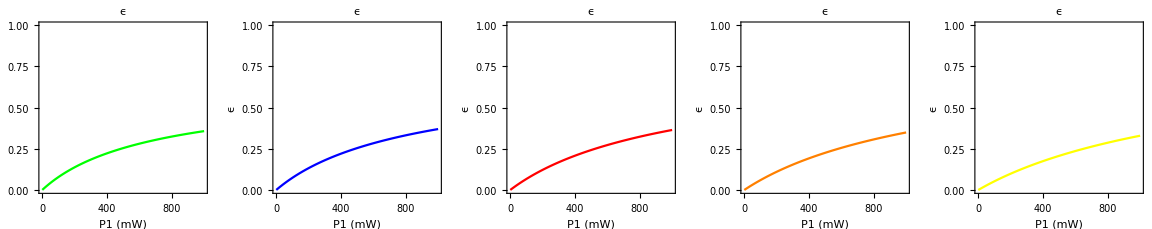

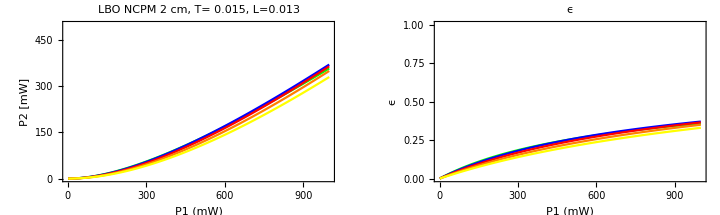

```mathematica
Clear[T1,loss,P2overP1,Enl,P1,P2,passes,P2out]


deff=.8 10^(-12);
n1=1.8;
n2=1.8;
lambda1=1.198 10^(-6);
lambda1=.99 10^(-6);
omega1=2 π cSI/lambda1;
Lc=0.02;
ENLbk=1.068 2 omega1^3 deff^2 Lc/(π epsilon0 cSI^4 n1 n2);
Print["ENLbk = ",ENLbk]

Print["Using ENL = ",ENLbk]
lossv1=2 .001 +0.0007+2 .005;
lossv1=2 .001 +0.001+2 .005 ;

label="LBO, 2 cm";

ENLbk=.6 ENLbk; (* corrction for walkoff *)

n1=1.57; n2=1.57; lambda1=1.54 10^-6;omega1=2 π cSI/lambda1;Lc=0.03;
parmsLBO1={header->"LBO NCPM 2 cm",Enl->ENLbk,T1->.03,loss->lossv1}
parmsLBO2={header->"LBO NCPM 2 cm",Enl->ENLbk,T1->.04,loss->lossv1}
parmsLBO3={header->"LBO NCPM 2 cm",Enl->ENLbk,T1->.05,loss->lossv1}

n1=1.57; n2=1.57; lambda1=.99 10^-6;omega1=2 π cSI/lambda1;Lc=0.02;
lossv1=3 .001 +0.001+2 .002   + 0.005; (* 3 good mirrors, xtal absorption, xtal coatings, excess *)
parmsLBO1={header->"LBO NCPM 2 cm",Enl->ENLbk,T1->.015,loss->lossv1}
parmsLBO2={header->"LBO NCPM 2 cm",Enl->ENLbk,T1->.02,loss->lossv1}
parmsLBO3={header->"LBO NCPM 2 cm",Enl->ENLbk,T1->.025,loss->lossv1}
parmsLBO4={header->"LBO NCPM 2 cm",Enl->ENLbk,T1->.03,loss->lossv1}
parmsLBO5={header->"LBO NCPM 2 cm",Enl->ENLbk,T1->.035,loss->lossv1}

(* --------------------------- choose parameter set ------------------------------------ *)
parms=parmsLBO1;
parmspower=parmsLBO1;
parmspower2=parmsLBO2;
parmspower3=parmsLBO3;
parmspower4=parmsLBO4;
parmspower5=parmsLBO5;
(* --------------------------------------------------------------------------------------- *)

eq={P2overP1==16  T1^2  Enl P1/(2-Sqrt[1-T1](2-loss- passes Sqrt[P2overP1  Enl P1]))^4};
p2maxinmw=5.;  (* max. output power for plotting *)
enlmax=.03; (* for plotting *)
passes=1 ;  (* 1 for unidirectional ring, 2 for bidirectional linear cavity *)
sol1=Solve[eq/.parms,{P2overP1}];

P1max=1000; P2max=.5 P1max;
P2out = P1 P2overP1/.Solve[eq/.parmspower,{P2overP1}][[1]];
plotlabel=StringJoin[header/.parmspower,", T= ",ToString[T1/.parmspower],", L=",ToString[loss/.parmspower]];
p1=Plot[10^3 P2out//.{P1->.001 P1mW} ,{P1mW,1,P1max},Frame->True,FrameLabel->{"P1 (mW)","P2 [mW]"},PlotLabel->plotlabel,PlotRange->{{0,P1max},{0, P2max}},BaseStyle->{FontWeight->"Bold",FontSize->12,FontFamily->"Arial"},FrameStyle->AbsoluteThickness[1.],Ticks->AbsoluteThickness[4.],PlotStyle->Green];
peps1=Plot[(P2out/P1)//.{P1->.001 P1mW} ,{P1mW,1,P1max},Frame->True,FrameLabel->{"P1 (mW)","ϵ"},PlotLabel->"ϵ",PlotRange->{{0,P1max},{0,1}},BaseStyle->{FontWeight->"Bold",FontSize->12,FontFamily->"Arial"},FrameStyle->AbsoluteThickness[1.],Ticks->AbsoluteThickness[4.],ImageSize->5 72,PlotStyle->Green];

P2out = P1 P2overP1/.Solve[eq/.parmspower2,{P2overP1}][[1]];
plotlabel=StringJoin[header/.parmspower2,", T= ",ToString[T1/.parmspower2],", L=",ToString[loss/.parmspower2]];
p2=Plot[10^3 P2out//.{P1->.001 P1mW} ,{P1mW,1,P1max},Frame->True,FrameLabel->{"P1 (mW)","P2 [mW]"},PlotLabel->plotlabel,PlotRange->{{0,P1max},{0, P2max}},BaseStyle->{FontWeight->"Bold",FontSize->12,FontFamily->"Arial"},FrameStyle->AbsoluteThickness[1.],Ticks->AbsoluteThickness[4.],PlotStyle->Blue];
peps2=Plot[(P2out/P1)//.{P1->.001 P1mW} ,{P1mW,1,P1max},Frame->True,FrameLabel->{"P1 (mW)","ϵ"},PlotLabel->"ϵ",PlotRange->{{0,P1max},{0,1}},BaseStyle->{FontWeight->"Bold",FontSize->12,FontFamily->"Arial"},FrameStyle->AbsoluteThickness[1.],Ticks->AbsoluteThickness[4.],PlotStyle->Blue,ImageSize->5 72];

P2out = P1 P2overP1/.Solve[eq/.parmspower3,{P2overP1}][[1]];
plotlabel=StringJoin[header/.parmspower3,", T= ",ToString[T1/.parmspower3],", L=",ToString[loss/.parmspower3]];
p3=Plot[10^3 P2out//.{P1->.001 P1mW} ,{P1mW,1,P1max},Frame->True,FrameLabel->{"P1 (mW)","P2 [mW]"},PlotLabel->plotlabel,PlotRange->{{0,P1max},{0, P2max}},BaseStyle->{FontWeight->"Bold",FontSize->12,FontFamily->"Arial"},FrameStyle->AbsoluteThickness[1.],Ticks->AbsoluteThickness[4.],PlotStyle->Red];
peps3=Plot[(P2out/P1)//.{P1->.001 P1mW} ,{P1mW,1,P1max},Frame->True,FrameLabel->{"P1 (mW)","ϵ"},PlotLabel->"ϵ",PlotRange->{{0,P1max},{0,1}},BaseStyle->{FontWeight->"Bold",FontSize->12,FontFamily->"Arial"},FrameStyle->AbsoluteThickness[1.],Ticks->AbsoluteThickness[4.],PlotStyle->Red,ImageSize->5 72];

P2out = P1 P2overP1/.Solve[eq/.parmspower4,{P2overP1}][[1]];
plotlabel=StringJoin[header/.parmspower4,", T= ",ToString[T1/.parmspower4],", L=",ToString[loss/.parmspower4]];
p4=Plot[10^3 P2out//.{P1->.001 P1mW} ,{P1mW,1,P1max},Frame->True,FrameLabel->{"P1 (mW)","P2 [mW]"},PlotLabel->plotlabel,PlotRange->{{0,P1max},{0, P2max}},BaseStyle->{FontWeight->"Bold",FontSize->12,FontFamily->"Arial"},FrameStyle->AbsoluteThickness[1.],Ticks->AbsoluteThickness[4.],PlotStyle->Orange];
peps4=Plot[(P2out/P1)//.{P1->.001 P1mW} ,{P1mW,1,P1max},Frame->True,FrameLabel->{"P1 (mW)","ϵ"},PlotLabel->"ϵ",PlotRange->{{0,P1max},{0,1}},BaseStyle->{FontWeight->"Bold",FontSize->12,FontFamily->"Arial"},FrameStyle->AbsoluteThickness[1.],Ticks->AbsoluteThickness[4.],PlotStyle->Orange,ImageSize->5 72];

P2out = P1 P2overP1/.Solve[eq/.parmspower5,{P2overP1}][[1]];
plotlabel=StringJoin[header/.parmspower5,", T= ",ToString[T1/.parmspower5],", L=",ToString[loss/.parmspower5]];
p5=Plot[10^3 P2out//.{P1->.001 P1mW} ,{P1mW,1,P1max},Frame->True,FrameLabel->{"P1 (mW)","P2 [mW]"},PlotLabel->plotlabel,PlotRange->{{0,P1max},{0, P2max}},BaseStyle->{FontWeight->"Bold",FontSize->12,FontFamily->"Arial"},FrameStyle->AbsoluteThickness[1.],Ticks->AbsoluteThickness[4.],PlotStyle->Yellow];
peps5=Plot[(P2out/P1)//.{P1->.001 P1mW} ,{P1mW,1,P1max},Frame->True,FrameLabel->{"P1 (mW)","ϵ"},PlotLabel->"ϵ",PlotRange->{{0,P1max},{0,1}},BaseStyle->{FontWeight->"Bold",FontSize->12,FontFamily->"Arial"},FrameStyle->AbsoluteThickness[1.],Ticks->AbsoluteThickness[4.],PlotStyle->Yellow,ImageSize->5 72];


buildup = T1/(1-Sqrt[1-loss])^2
Print[label] 
Print["w BK = ",10^6 Sqrt[lambda1 Lc/(5.68 π n1)]," (μm)"]
Print["ENL BK optimum = ",ENLbk]
Print["Power build up factor in cavity (no SHG generated) = ",buildup//.parms]
GraphicsRow[{p1,p2,p3,p4,p5},ImageSize->16 72]
GraphicsRow[{peps1,peps2,peps3,peps4,peps5},ImageSize->16 72]
p1=Show[p1,p2,p3,p4,p5,ImageSize->5 72,PlotRange->{{0,P1max},{0, P2max}}];
p2=Show[peps1,peps2,peps3,peps4,peps5,ImageSize->5 72,PlotRange->{{0,P1max},{0,1}}];
GraphicsRow[{p1,p2},ImageSize->10 72]
```

```mathematica
2 cm ppktp 37% absorption at 410 nm  mesaured by Jinlu 2012.02.24
```

```mathematica
(100*10^-6*.5*10^-3 π)/(824*10^-9)*10^3
```

190.631